```mathematica
Manipulate[∑_(i=1)^n i^(1/2),{n,1,k,1},{k,1,50}]
```

```mathematica
Manipulate[N[∑_(i=1)^n i^(1/2)], {n,1,k,1}, {k,1,50}]
```

General::stop: Further output of DecimalForm::iprf will be suppressed during this calculation.

DecimalForm::argct: DecimalForm called with 3 arguments.

```mathematica
Manipulate[∑_(t=1)^n Gamma[t+1]/Gamma[t+1/2],{n,1,k,1},{k,1,50}]
```

```mathematica
N[Manipulate[∑_(t=1)^n Gamma[t+1]/Gamma[t+1/2],{n,1,k,1},{k,1,50}]]
```

NSum::nslim: Limit of summation n is not a number.

```mathematica
N[Manipulate[∑_(i=1)^n i^(1/2),{n,1,k,1},{k,1,50}]]
```

NSum::nslim: Limit of summation n is not a number.

```mathematica
N[Manipulate[∑_(t=1)^n Gamma[t+1]/Gamma[t+1/2],{n,1,k,1},{k,1,50}]]
```

NSum::nslim: Limit of summation n is not a number.

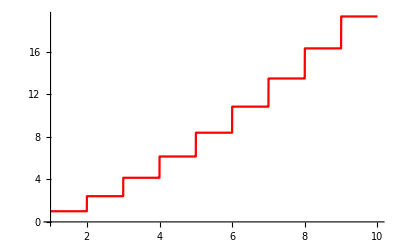

```mathematica
p1=Plot[∑_(i=1)^n i^(1/2),{n,1,10},PlotStyle->Red]
```

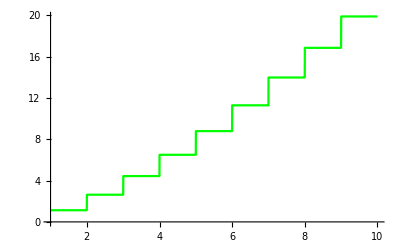

```mathematica
p2=Plot[∑_(t=1)^n Gamma[t+1]/Gamma[t+1/2],{n,1,10},PlotStyle->Green]
```

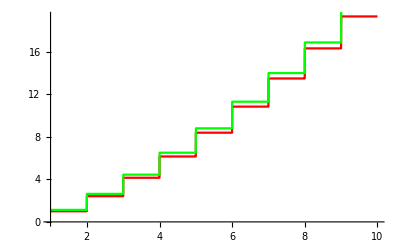

```mathematica
Show[p1,p2]
```

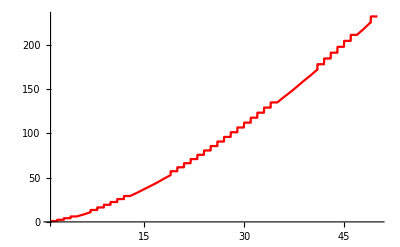

```mathematica
p3=Plot[∑_(i=1)^n i^(1/2),{n,1,50},PlotStyle->Red]
```

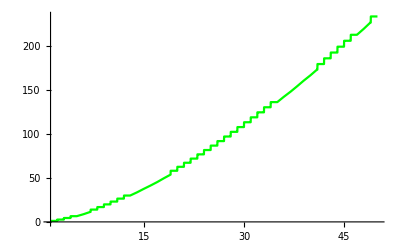

```mathematica
p4=Plot[∑_(t=1)^n Gamma[t+1]/Gamma[t+1/2],{n,1,50},PlotStyle->Green]
```

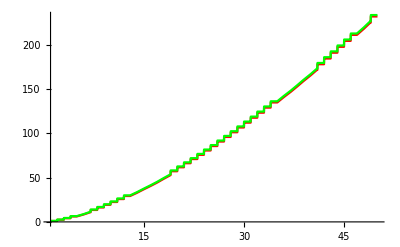

```mathematica
Show[p3,p4]
```

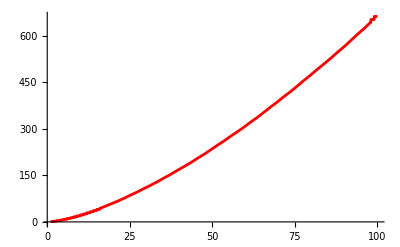

```mathematica
p5=Plot[∑_(i=1)^n i^(1/2),{n,1,100},PlotStyle->Red]
```

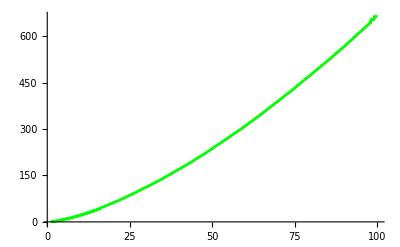

```mathematica
p6=Plot[∑_(t=1)^n Gamma[t+1]/Gamma[t+1/2],{n,1,100},PlotStyle->Green]
```

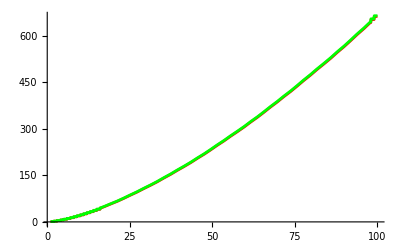

```mathematica
Show[p5,p6]
```

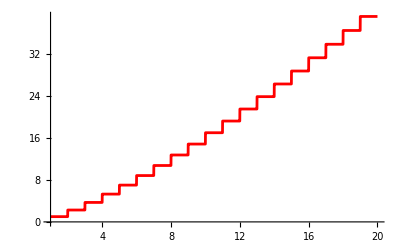

```mathematica
p7=Plot[∑_(i=1)^n i^(1/3),{n,1,20},PlotStyle->Red]
```

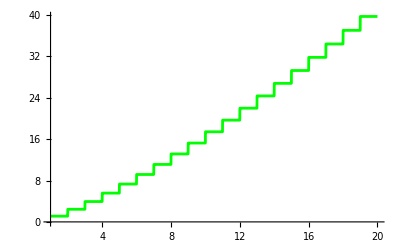

```mathematica
p8=Plot[∑_(t=1)^n Gamma[t+1]/Gamma[t+2/3],{n,1,20},PlotStyle->Green]
```

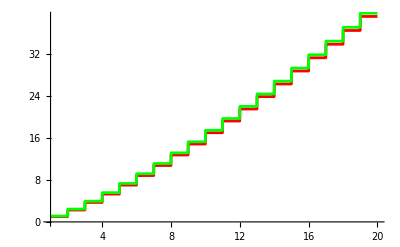

```mathematica
Show[p7,p8]
```

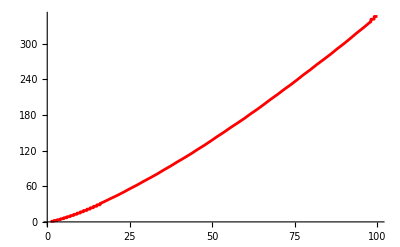

```mathematica
p9=Plot[∑_(i=1)^n i^(1/3),{n,1,100},PlotStyle->Red]
```

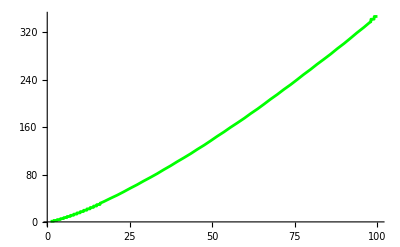

```mathematica
p10=Plot[∑_(t=1)^n Gamma[t+1]/Gamma[t+2/3],{n,1,100},PlotStyle->Green]
```

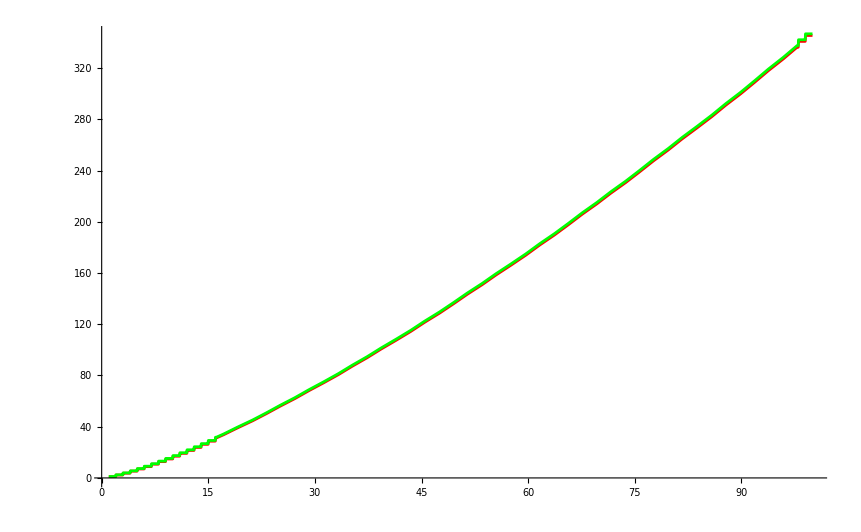

```mathematica
Show[p9,p10]
```

```mathematica
The below does not work, i.e. multiply by reciprocal of 2/(√π)
```

```mathematica
Manipulate[∑_(t=1)^n Gamma[t+1]/Gamma[t-1/2],{n,1,k,1},{k,1,50}]
```

```mathematica
Manipulate[N[∑_(t=1)^n Gamma[t+1]/Gamma[t+3/2]],{n,1,k,1},{k,1,1000}]
```

```mathematica
Manipulate[N[∑_(i=1)^n i^(-1/2)], {n,1,k,1}, {k,1,1000}]
```

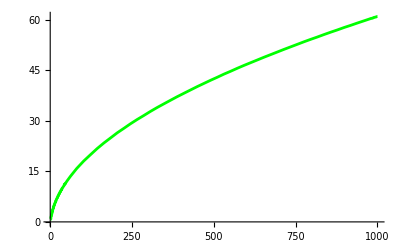

```mathematica
p11=Plot[∑_(t=1)^n Gamma[t+1]/Gamma[t+3/2],{n,1,1000},PlotStyle->Green]
```

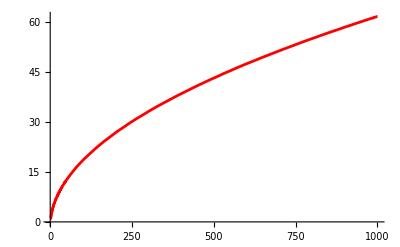

```mathematica
p12=Plot[∑_(i=1)^n i^(-1/2),{n,1,1000},PlotStyle->Red]
```

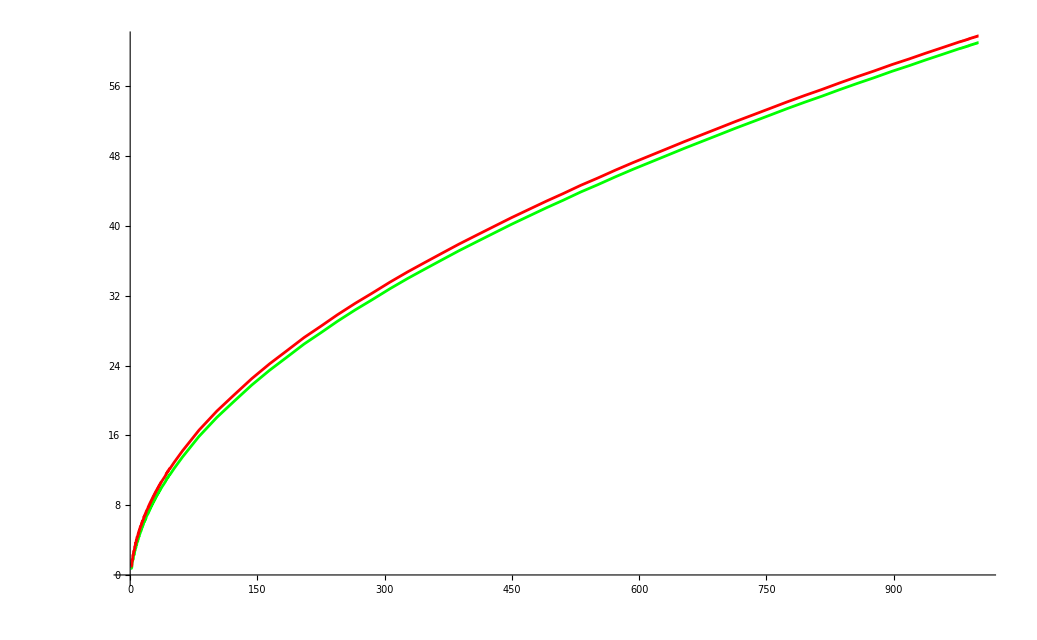

```mathematica
Show[p11,p12]
```